William Kessel
105B
204839956

```mathematica
Remove["Global`*"];
y1[x_,t_]=A1 Sin[k1(x-v t)];
y2[x_,t_]=A2 Sin[k2(x +v t)];
yr[x_,t_]=y1[x,t]+y2[x,t];
k2=k1+δk;
A1=2;
A2=2;
v=1;
k1=10π;
δk=.25k1;

xmax=5;
pix1[t_]:=Plot[y1[x,t],{x,0,xmax},PlotStyle->Red]
pix2[t_]:=Plot[5+y2[x,t],{x,0,xmax},PlotStyle->Blue]
pixr[t_]:=Plot[10+yr[x,t],{x,0,xmax},PlotStyle->Black]
plot[t_]:=Show[pix1[t],pix2[t],pixr[t], PlotRange->{{0,xmax},{-4,18}}];
Animate[plot[t],{t,0,50}]
```

```mathematica
Remove["Global`*"];
y1[x_,t_]=A1 Sin[k1(x-v t)];
y2[x_,t_]=A2 Sin[k2(x +v t)];
yr[x_,t_]=y1[x,t]+y2[x,t];
k2=k1+δk;
A1=1;
A2=2;
v=1;
k1=2π/(5*2);
δk=.5;

xmax=5;

pixr[t_]:=Plot[yr[x,t],{x,0,xmax},PlotStyle->Black]
plot[t_]:=Show[pixr[t], PlotRange->{{0,xmax},{-4,18}}];
Animate[plot[t],{t,0,20}]

Print["you would hear beats"]
```

you would hear beats

Solving the Marion Problem: Ψ[x,t] = (2 ⅇ^(-ⅈ k0 x+ⅈ t ω0) Sin[Δk (x-t ω0p)])/(x-t ω0p)

A(k)=1

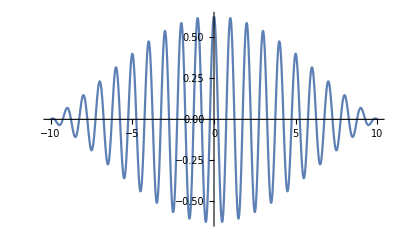

B(k) = DiracDelta[k − k0]

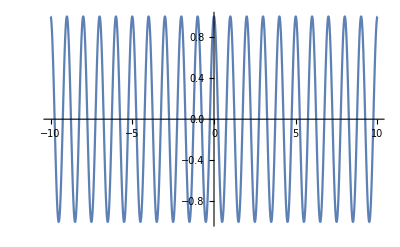

CC(k) = cos ( π2Δk(k − k0))

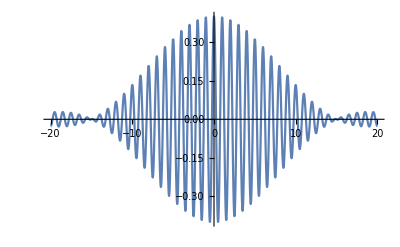

DD(k) = (k−k0+Δk)/(2Δk)

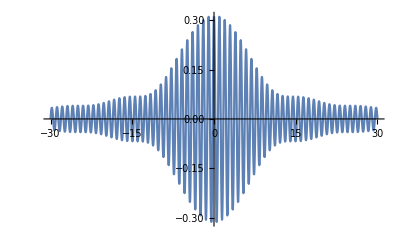

EE(k) = (k−k0)^2/(Δk)^2;

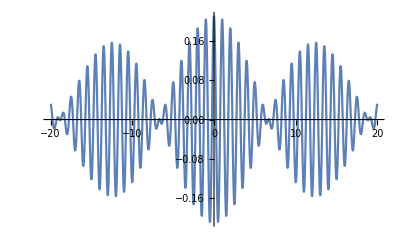

```mathematica
Remove["Global`*"];

SetAttributes[{k0,ω0,δk,ω0p},Constant];
$Assumptions={Element[{k0,ω0,Δk,ω0p,t},Reals] && k0>0 && ω0>0 && δk >0};

(*coefficients*)
A[k_]=1;
B[k_]=DiracDelta[k-k0];
CC[k_]=Cos[π/(2 Δk) (k-k0)];
DD[k_]=(k−k0+Δk)/(2Δk);
EE[k_]=(k−k0)^2/(Δk)^2;

klo=k0-Δk;
khi=k0+Δk;
ω = ω0 + ω0p (k-k0);

(*wave functions*)
Ψ[x_,t_]=Integrate[ A[k] E^(I (ω t - k x)),{k,klo,khi}]//Simplify;
Ψ2[x_,t_]=Integrate[ B[k] E^(I (ω t - k x)),{k,-Infinity,Infinity}]//Simplify;
Ψ3[x_,t_]=Integrate[ CC[k] E^(I (ω t - k x)),{k,klo,khi}]//Simplify;
Ψ4[x_,t_]=Integrate[ DD[k] E^(I (ω t - k x)),{k,klo,khi}]//Simplify;
Ψ5[x_,t_]=Integrate[ EE[k] E^(I (ω t - k x)),{k,klo,khi}]//Simplify;

(*answering the book question*)
Print["\n\nSolving the Marion Problem: Ψ[x,t] = ",Ψ[x,t]]
(**************************************)
SuperStar[z_] :=Conjugate[z];


k0 = 2 π;
Δk =  0.1 π;
ω0 = 0.2 π;
ω0p = 0.3 π;

(*Plots*)
A[x_,t_]=1/2 (Ψ[x,t] +SuperStar[Ψ[x,t]])//Simplify;
Print["\n\nA(k)=1 "];
Plot[A[x,0],{x,-10,10},PlotRange->All]

B[x_,t_]=1/2 (Ψ2[x,t] +SuperStar[Ψ2[x,t]])//Simplify;
Print["\n\nB(k) = DiracDelta[k − k0]"]
Plot[B[x,0],{x,-10,10},PlotRange->All]

CC[x_,t_]=1/2 (Ψ3[x,t] +SuperStar[Ψ3[x,t]])//Simplify;
Print["\n\nCC(k) = cos ( π2Δk(k − k0)) "]
Plot[CC[x,0],{x,-20,20},PlotRange->All]

DD[x_,t_]=1/2 (Ψ4[x,t] +SuperStar[Ψ4[x,t]])//Simplify;
Print["\n\nDD(k) = (k−k0+Δk)/(2Δk) "]
Plot[DD[x,0],{x,-30,30},PlotRange->All]

EE[x_,t_]=1/2 (Ψ5[x,t] +SuperStar[Ψ5[x,t]])//Simplify;
Print["\n\nEE(k) = (k−k0)^2/(Δk)^2;"]
Plot[EE[x,0],{x,-20,20},PlotRange->All]
```

```mathematica
Remove["Global`*"];

q[1][x_]= 3 a  x/( L);
xlo[1]=0;
xhi[1]= L/3;

q[2][x_]=(3h/2L )(L-x);

xlo[2]=xhi[1];
xhi[2]= L;

b[n_]= 2/L Sum[Integrate[q[i][x] Sin[n π x/L],{x,xlo[i],xhi[i]}],{i,1,2}]//Refine//Simplify;


blist=Table[{n,b[n]},{n,1,2}];
wave[x_,t_]=Sum[b[n] Sin[n π x/L] Cos[n π vx/L t],{n,1,2}];
wave[x,0]==0;

Print["q(x,t)= ",wave[x,t]//Simplify]
```

q(x,t)= 1/(8 π^2)(4 (a (6 √3-2 π)+h L^2 (3 √3+2 π)) Cos[(π t vx)/L] Sin[(π x)/L]+(h L^2 (3 √3-4 π)+a (6 √3+4 π)) Cos[(2 π t vx)/L] Sin[(2 π x)/L])

c[ω]= (ⅇ^(-ω^2/(4 α)) n)/(√2 √α)

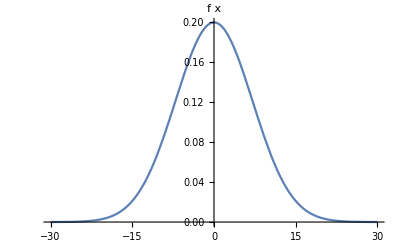

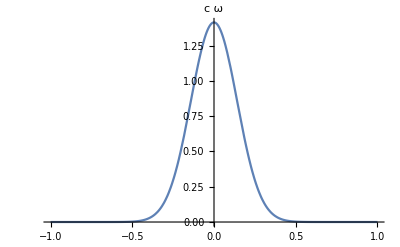

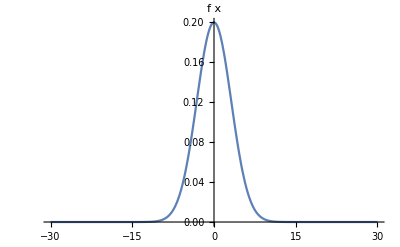

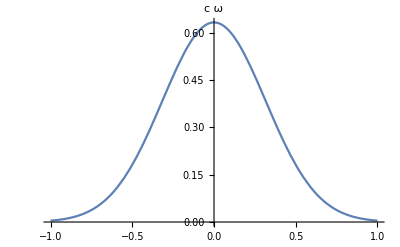

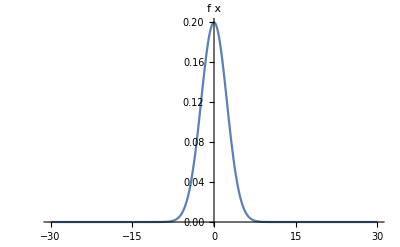

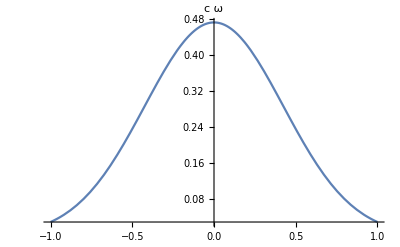

d[ω]= (√(2/π) Sin[a ω])/ω

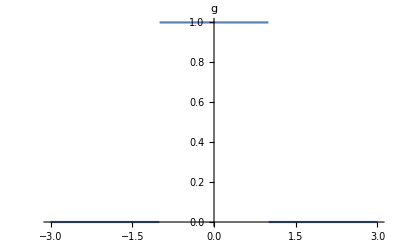

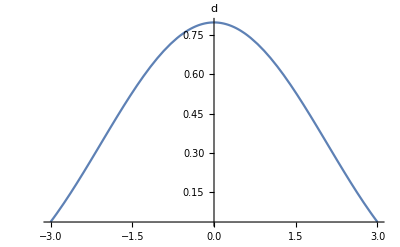

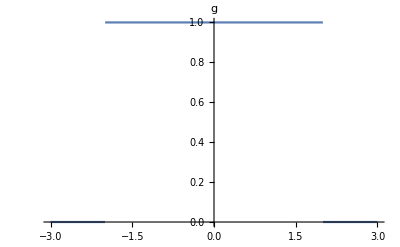

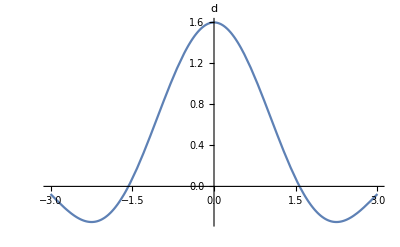

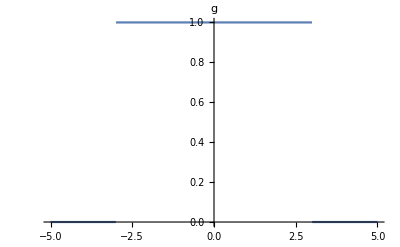

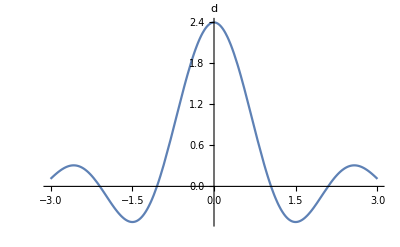

As the spread in x increases, the spread in p decreases

```mathematica
Remove["Global`*"];

f[x_]=n E^(-α x^2);
c[ω_] = FourierTransform[f[x],x,ω]//Refine//Simplify;
Print["c[ω]= ",c[ω]]

n=.2;
α=.01;

Plot[f[x], {x,-30,30},PlotRange->All,AxesLabel->f(x)]
Plot[c[ω],{ω,-1,1},PlotRange->All,AxesLabel->c(ω)]
α=.05;
Plot[f[x], {x,-30,30},PlotRange->All,AxesLabel->f(x)]
Plot[c[ω],{ω,-1,1},AxesLabel->c(ω)]
α=.09;
Plot[f[x], {x,-30,30},PlotRange->All,AxesLabel->f(x)]
Plot[c[ω],{ω,-1,1},PlotRange->All,AxesLabel->c(ω)]

g[x_]= -HeavisideTheta[x-a]+HeavisideTheta[x+a];
d[ω_] = FourierTransform[g[x],x,ω]//Refine//Simplify;

Print["d[ω]= ",d[ω]]
a=1;
Plot[g[x], {x,-3,3},PlotRange->All,AxesLabel->g]
Plot[d[ω],{ω,-3,3},PlotRange->All,AxesLabel->d ]
a=2;
Plot[g[x], {x,-3,3},PlotRange->All,AxesLabel->g ]
Plot[d[ω],{ω,-3,3},PlotRange->All,AxesLabel->d ]
a=3;
Plot[g[x], {x,-5,5},PlotRange->All,AxesLabel->g  ]
Plot[d[ω],{ω,-3,3},PlotRange->All,AxesLabel->d ]
Print["As the spread in x increases, the spread in p decreases"]
```

```mathematica
Remove["Global`*"];

$Assumptions={Element[{ωo,ω,t},Reals] && ω0>0 && ω>0 &&ω1>0 && ω2 >0&& ω1-ω2 >0&&t0>0 &&Δt>0};

y1[t_]=Sin[ω0 t];
c[ω_] = FourierTransform[y1[t],t,ω]//Refine//Simplify;

Print["\nThe spectral decomposition of y1[t]=" , y1[t]]
Print["is c[ω] = ",c[ω]]

y2[t_]=Sin[ω1 t] Sin[ω2 t];
d[ω_]= FourierTransform[y2[t],t,ω]//Refine//Simplify;

Print["\nThe spectral decomposition of y2[t]=" , y2[t]]
Print["is d[ω] = ",d[ω]]
```

The spectral decomposition of y1[t]=Sin[t ω0]

is c[ω] = ⅈ √(π/2) DiracDelta[ω-ω0]

The spectral decomposition of y2[t]=Sin[t ω1] Sin[t ω2]

is d[ω] = -1/2 √(π/2) DiracDelta[ω-ω1-ω2]+1/2 √(π/2) DiracDelta[ω-ω1+ω2]